# Exact Control Variate

## - Using Schwinger-Dyson Equations

## Single Plaquette U(1) Action

```mathematica
SinglePlaquetteOneD[beta_, bdvalue_]:=Module[{Action, Z, WilsonLoop, Variance, G, exactG, y, solG, CV,meanCV, VarianceReduced},
(* 1 Plaquette Action *)
Action[x_]:=beta*(1-Cos[x]);
(* Partition Function *)
(*Z                     :=Integrate[Exp[-Action[x]],{x,0,2*Pi}];*)
Z := 2 ⅇ^-beta π BesselI[0,beta];
(* Wilson Loop *)
(*WilsonLoop :=Integrate[Cos[x]Exp[-Action[x]],{x,0,2*Pi}]/Z;*)
WilsonLoop :=BesselI[1,beta]/BesselI[0,beta];
(* Variance *)
(*Variance      := Integrate[Cos[x]^2Exp[-Action[x]],{x,0,2*Pi}]/Z - WilsonLoop^2;*)
Variance := -BesselI[1,beta]^2/BesselI[0,beta]^2+(BesselI[1,beta]+beta BesselI[2,beta])/(beta BesselI[0,beta]);
(* Solve the Schwinger Dyson Differential Function for G function *)
(*Print[Z];
Print[WilsonLoop];
Print[Variance];*)

(*Schwinger Dyson Equation*)
exactG:= DSolve[{y'[x] -y[x] * beta * Sin[x] == Cos[x] + WilsonLoop, y[0]==bdvalue}, y, x];
y[x_]=y[x]/.exactG;
(*Define the function inside the integral*)
integrand[k_]:=Exp[beta (Cos[k])]*(-WilsonLoop+Cos[k]);
    
(*Define the overall function using a numerical integral*)
f[x_]:=Exp[-beta (Cos[x])]*NIntegrate[integrand[k],{k,0,x}];

solG :=NDSolve[{G'[x] -G[x] * beta * Sin[x] == Cos[x] - WilsonLoop, G[Pi]==bdvalue}, G, {x,0,6*Pi}];
(* Control Variate CV *)
CV[x_]:=G'[x] - G[x]*beta*Sin[x]/.solG;
meanCV:=NIntegrate[CV[x]*Exp[-Action[x]],{x,0,2*Pi}]/Z;
(* Return the mean CV*)
Print[y[x]];
Print["Integration of the Control Variate: ",meanCV];

(* Variance Reduced *)
VarianceReduced:= NIntegrate[(Cos[x]-CV[x])^2Exp[-Action[x]],{x,0,2*Pi}]/Z - (WilsonLoop - (meanCV))^2;
(* Return the Variance, VarianceReduced *)
Print["Variance :", Variance, ", Variance Reduced: ", VarianceReduced];

(* Plot the CV *)
Ploty=Plot[{Cos[x]-WilsonLoop,Evaluate[CV[x]],Exp[-Action[x]]/Z},{x,0,2*Pi},PlotRange->All];
(*Ploty=Plot3D[f[x,y],{x,0,2Pi},{y,0,2Pi},PlotRange->All];*)
PlotG=Plot[Evaluate[G[x]/.solG], {x,0,2*Pi}, PlotRange->All];
PlotCV=Plot[Exp[-Action[x]]/Z, {x,0,4*Pi}, PlotRange->All];
CellPrint@ExpressionCell[#,"Output"]&/@{Ploty, PlotG, PlotCV};
]
```

{ⅇ^(-5.55 Cos[x]) 1. ⅇ^(5.55 Cos[K[1]]) (0.904747+1. Cos[K[1]])K[1]0x}

Integration of the Control Variate: {1.32002×10^-9}

Variance :0.0184147, Variance Reduced: {5.66214×10^-14}

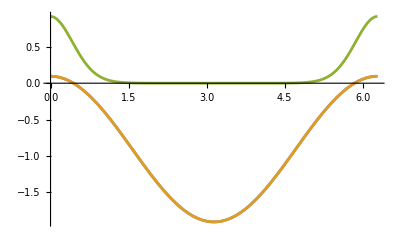

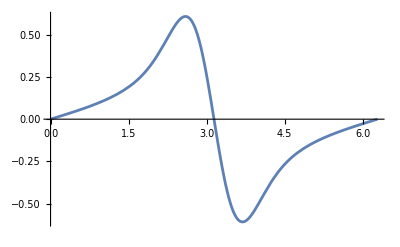

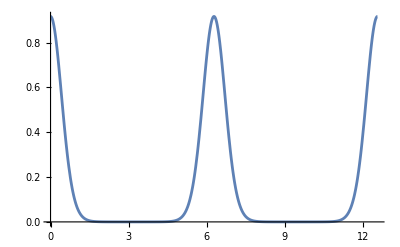

```mathematica
SinglePlaquetteOneD[5.55, 0]
```

## Double Plaquette U(1) Action

```mathematica
DoublePlaquetteOneD[beta_, bdvalue_]:=Module[{Action, Z, WilsonLoop, WilsonLoop1loop, Variance, exactG, G, G1loop,solG, CV,meanCV, VarianceReduced},
(* 2 Plaquette Action *)
Action[x_, y_]:=beta*(1-Cos[x]-Cos[y]);
(* Partition Function *)
(*Z                     :=Integrate[Exp[-Action[x,y]],{x,0,2*Pi},{y,0,2*Pi}];*)
Z := 4 ⅇ^-beta π^2 BesselI[0,beta]^2;
(* Wilson Loop *)
(*WilsonLoop :=Integrate[Cos[x+y]Exp[-Action[x, y]],{x,0,2*Pi}, {y,0,2*Pi}]/Z;*)
WilsonLoop            :=BesselI[1,beta]^2/BesselI[0,beta]^2;
WilsonLoop1loop :=BesselI[1,beta]/BesselI[0,beta];
(* Variance *)
(*Variance      := Integrate[Cos[x+y]^2Exp[-Action[x,y]],{x,0,2*Pi},{y,0,2*Pi}]/Z - WilsonLoop^2;*)
Variance := -BesselI[1,beta]^4/BesselI[0,beta]^4+(-BesselI[1,beta] BesselI[2,beta]+BesselI[0,beta] (BesselI[1,beta]+beta BesselI[2,beta]))/(beta BesselI[0,beta]^2);
(* Solve the Schwinger Dyson Differential Function for G function *)
(*Print[Z];
Print[WilsonLoop];
Print[Variance];*)

(*Schwinger Dyson Equation*)
(*solG1loop :=NDSolve[{G1loop'[x] -G1loop[x] * beta * Sin[x] == Cos[x] - WilsonLoop1loop, G1loop[0]==bdvalue}, G1loop, {x,0,2*Pi}];*)
(*G1loop[x_]:=Exp[-beta*Cos[x]]*NIntegrate[Exp[beta*Cos[y]]*(WilsonLoop1loop-Cos[y]),{y,0,x}];*)
(*G2loop[x_]:=Exp[-beta*Cos[x]]*NIntegrate[Exp[beta*Cos[y]]*(WilsonLoop1loop+Cos[y]),{y,0,x}];*)
(*solG2loop :=NDSolve[{G2loop'[x] -G2loop[x] * beta * Sin[x] == Cos[x] + WilsonLoop1loop, G2loop[0]==bdvalue}, G2loop, {x,0,2*Pi}];*)

(*solG1:=NDSolve[{D[G1[x,y],x] -G1[x,y] * beta * Sin[x] == Cos[x+y] - WilsonLoop, G1[0,y]==bdvalue, G1[x,0]==bdvalue,G1[2*Pi,y]==bdvalue, G1[x,2*Pi]==bdvalue}, G1, {x,0,2*Pi},{y,0,2*Pi}];*)
(*solG2:=NDSolve[{D[G2[x,y],y] -G2[x,y] * beta * Sin[y] == Cos[x+y] - WilsonLoop, G2[0,y]==bdvalue, G2[x,0]==bdvalue, G2[2*Pi,y]==bdvalue, G2[x,2*Pi]==bdvalue}, G2, {x,0,2*Pi},{y,0,2*Pi}];*)
(*solG:=NDSolve[{D[G[x,y],x] -G[x,y] * beta * Sin[x] == Cos[x+y] - WilsonLoop,G[Pi,y]==bdvalue}, G, {x,0*Pi,2*Pi},{y,0*Pi, 2*Pi}];*)
(*exactG:=DSolve[{D[G[x,y],x] -G[x,y] * beta * Sin[x] == Cos[x+y] - WilsonLoop, G[Pi,y]==bdvalue }, G, x,y];
G1loop[x_,y_]:=G[x,y]/.exactG;
Print[G1loop[x,y]];*)
(*G[x_,y_]:=Exp[-beta*(Cos[x])]*NIntegrate[Exp[beta*(Cos[u])]*(WilsonLoop-Cos[u+y]),{u,0,x}];*)
(* Control Variate CV *)
(*CV[x_,y_]:=(D[G[x,y],x] -G[x,y] * beta * Sin[x])+(D[G[x,y],y] -G[x,y] * beta * Sin[y]);*)
CV[x_,y_]:=(Cos[x+y])- WilsonLoop;

(*CV[x_,y_]:=(D[G[x,y],x] -G[x,y] * beta * Sin[x])/.solG;*)
(*CV[x_,y_]:=(D[G[x,y],x] -G[x,y] * beta * Sin[x])+(D[G[x,y],y] -G[x,y] * beta * Sin[y]);*)
(*CV[x_,y_]:=(D[G2[x,y],y] -G2[x,y] * beta * Sin[y])/.solG2;*)
meanCV:=NIntegrate[(CV[x,y])*Exp[-Action[x,y]],{x,0,2*Pi},{y,0,2*Pi}]/Z;
(* Return the mean CV*)
Print["Integration of the Control Variate: ",meanCV];
(*Print["Alternating signs:",FindRoot[(Cos[x+y])==0,{{x,0},{y,0}}]];*)

(* Variance Reduced *)
VarianceReduced:= NIntegrate[(Cos[x+y]-CV[x,y])^2Exp[-Action[x,y]],{x,0,2*Pi},{y,0,2*Pi}]/Z - (WilsonLoop-meanCV)^2;
(* Return the Variance, VarianceReduced *)
Print["Variance :", Variance, ", Variance Reduced: ", VarianceReduced];

(* Plot the CV *)
(*Ploty=Plot[{Cos[x]-WilsonLoop,Evaluate[CV[x]],Exp[-Action[x]]/Z},{x,0,2*Pi},PlotRange->All];*)
(*Ploty=Plot3D[f[x,y],{x,0,2Pi},{y,0,2Pi},PlotRange->All];*)
(*PlotG=Plot[Evaluate[G[x]/.solG], {x,0,4*Pi}, PlotRange->All];*)
(*PlotCVtest=Plot3D[{ Evaluate[G[x,y]/.solG]}, {x,-4*Pi,4*Pi},{y,-4*Pi,4*Pi}, PlotRange->All, PlotLegends->Automatic];*)
PlotG1 = Plot3D[{(Exp[-Action[x,y]]/Z)*Cos[x+y]^2,z=0}, {x,-2*Pi,2*Pi},{y,-2*Pi,2*Pi}, PlotRange->All];
PlotG2 = Plot3D[{(Exp[-Action[x,y]]/Z),(Cos[x+y]-WilsonLoop),z=0}, {x,-2*Pi,2*Pi},{y,-2*Pi,2*Pi}, PlotRange->All];
(*PlotG2 = ContourPlot[Evaluate[CV[x,y]], {x,0-4Pi,4*Pi},{y,-4*Pi,4*Pi}, PlotRange->All];*)
(* Plot the CV *)
(*PlotG1=Plot3D[Evaluate[G1[x,y]/.solG1], {x,0,2*Pi}, {y,0,2*Pi},PlotRange->All];|
PlotG2=Plot3D[Evaluate[G2[x,y]/.solG2], {x,0,2*Pi}, {y,0,2*Pi},PlotRange->All];*)
(*PlotG1loop=Plot[Evaluate[G1loop[x]], {x,0,2*Pi}, PlotRange->All];*)
(*PlotG=Plot3D[Evaluate[G[x,y]], {x,0,2*Pi}, {y,0,2*Pi},PlotRange->All];|*)
(*PlotG=Plot3D[Evaluate[G[x,y]/.solG], {x,0,2*Pi}, {y,0,2*Pi},PlotRange->All];*)
(*PlotCV=ContourPlot[Evaluate[CV[x,y]], {x,0,2*Pi},{y,0,2*Pi}, PlotRange->All];*)
CellPrint@ExpressionCell[#,"Output"]&/@{ PlotG1,PlotG2};
]
```

```mathematica
DoublePlaquetteOneD[5.55, 0.00]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02189×10^-13 and 7.64426×10^-10 for the integral and error estimates.

Integration of the Control Variate: 1.31336×10^-15

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.02189×10^-13 and 7.64426×10^-10 for the integral and error estimates.

Variance :0.0570612, Variance Reduced: -3.12585×10^-9

-Graphics3D-

-Graphics3D-

## Single Plaquette (Link picture)

```mathematica
SinglePlaquetteOneDlink[beta_, bdvalue_]:=Module[{Action, Z, WilsonLoop, Variance, G, exactG, y, solG, CV,meanCV, VarianceReduced},
(* 1 Plaquette Action *)
Action[a_,b_,c_,d_]:=beta*(1-Cos[a+b+c+d]);
(* Partition Function *)
(*Z                     :=Integrate[Exp[-Action[a,b,c,d]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}];*)
Z := 16 ⅇ^-beta π^4 BesselI[0,beta];
(* Wilson Loop *)
(*WilsonLoop :=Integrate[Cos[a+b+c+d]Exp[-Action[a,b,c,d]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}]/Z;*)
WilsonLoop :=BesselI[1,beta]/BesselI[0,beta];
(* Variance *)
(*Variance      := Integrate[Cos[a+b+c+d]^2Exp[-Action[a,b,c,d]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}]/Z - WilsonLoop^2;*)
Variance :=(beta BesselI[0,beta]-BesselI[1,beta])/(beta BesselI[0,beta])-BesselI[1,beta]^2/BesselI[0,beta]^2 ;
VarianceReduced:=Integrate[Exp[-Action[a,b,c,d]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}]/Z;
(* Solve the Schwinger Dyson Differential Function for G function *)
Print[Z];

Print[WilsonLoop];
Print[Variance];
y[x_]:=Exp[-beta*Cos[x]]Integrate[Exp[beta*Cos[t]]*(Cos[t]-WilsonLoop),{t,0,x}];
(*Schwinger Dyson Equation*)
(*solG:=NDSolve[{D[G[a,b,c,d],a]+D[G[a,b,c,d],b] +D[G[a,b,c,d],c] +D[G[a,b,c,d],d]  -G[a,b,c,d] * beta * 4*Sin[a+b+c+d] == Cos[a+b+c+d] - WilsonLoop,
G[0,0,0,0]                       ==0, 
G[0,2Pi,0,0]                  ==0,
G[0,0,2Pi,0]                  ==0,
 G[0,0,0,2Pi]                 ==0,
G[2Pi,2Pi, 2Pi, 2Pi]==0,
(*Dirichlet boundary conditions*)
G[a,0,0,0]==y[a],
G[a,2 Pi,0,0]==y[a],
G[a,0,2 Pi,0]==y[a],
G[a,0,0,2 Pi]==y[a]
}, G, {a,0,2*Pi},{b,0, 2*Pi},{c,0,2*Pi},{d,0,2*Pi}];
Print[solG];*)
(*Ploty=Plot[y[x],{x,0,2*Pi},PlotRange->All];
CellPrint@ExpressionCell[#,"Output"]&/@{ Ploty};*)
]
```

```mathematica
SinglePlaquetteOneDlink[5.55, 0]
```

270.642

0.904747

0.0184147

NDSolve::bcedge: Boundary condition G$3786252[0,0,0,0]==0 is not specified on a single edge of the boundary of the computational domain.

NDSolve[{-22.2 G$3786252[a,b,c,d] Sin[a+b+c+d]+G$3786252^(0,0,0,1)[a,b,c,d]+G$3786252^(0,0,1,0)[a,b,c,d]+G$3786252^(0,1,0,0)[a,b,c,d]+G$3786252^(1,0,0,0)[a,b,c,d]==-0.904747+Cos[a+b+c+d],G$3786252[0,0,0,0]==0,G$3786252[0,2 π,0,0]==0,G$3786252[0,0,2 π,0]==0,G$3786252[0,0,0,2 π]==0,G$3786252[2 π,2 π,2 π,2 π]==0,G$3786252[a,0,0,0]==ⅇ^(-5.55 Cos[a]) ∫_0^a ⅇ^(5.55 Cos[t]) (-0.904747+Cos[t])ⅆt,G$3786252[a,2 π,0,0]==ⅇ^(-5.55 Cos[a]) ∫_0^a ⅇ^(5.55 Cos[t]) (-0.904747+Cos[t])ⅆt,G$3786252[a,0,2 π,0]==ⅇ^(-5.55 Cos[a]) ∫_0^a ⅇ^(5.55 Cos[t]) (-0.904747+Cos[t])ⅆt,G$3786252[a,0,0,2 π]==ⅇ^(-5.55 Cos[a]) ∫_0^a ⅇ^(5.55 Cos[t]) (-0.904747+Cos[t])ⅆt},G$3786252,{a,0,2 π},{b,0,2 π},{c,0,2 π},{d,0,2 π}]

## Double Plaquette Link picture

```mathematica
DoublePlaquetteOneDlink[beta_, bdvalue_, st1_, st2_]:=Module[{Action, Z, WilsonLoop,Variance, G, exactG, y, solG, CV,meanCV, VarianceReduced},
(*2 Plaquette Action*)
Action[x_]:=beta*(1-Cos[st1+x]-Cos[st2-x]);
WilsonLoop            :=BesselI[1,beta]^2/BesselI[0,beta]^2;
solG:=NDSolve[{G'[x]-beta*G[x]*(Sin[st1+x]-Sin[st2-x])==Cos[st1+st2]-WilsonLoop, G[0]==0},G, {x,0*Pi,2*Pi}];
(*exactG:=DSolve[{y'[x]-beta*y[x]*(Sin[st1+x]-Sin[st2-x])==Cos[st1+st2]-WilsonLoop, y[0]== bdvalue},y, x];*)
(*solG:=NDSolve[{D[G[x,y,z],x]-beta*G[x,y,z]*(Sin[y+x]-Sin[z-x])==Cos[y+z]-WilsonLoop, G[0,0,0]==bdvalue, G[0,y,z]==0},G, {x,0,2*Pi},{y,0,2*Pi},{z,0,2*Pi}];*)
(*Print[y[x]/.exactG];*)
(*y[x_]:=y[x]/.exactG;
Print[y[x]];*)
PlotG=Plot[Evaluate[G[x]/.solG],{x,0*Pi,2*Pi},PlotRange->All];
CellPrint@ExpressionCell[#,"Output"]&/@{ PlotG};
]
```

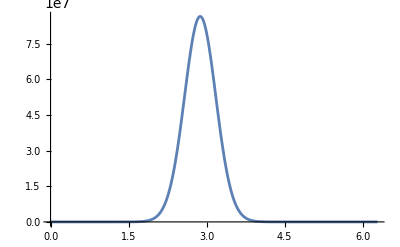

```mathematica
DoublePlaquetteOneDlink[5.55,0, 0.38020312786102295, -0.15121829509735107]
```

```mathematica
ClearAll[f]
f[beta_,st1_,st2_,x_]:=E^(-beta Cos[st1] Cos[x]-beta Cos[st2] Cos[x]+beta Sin[st1] Sin[x]-beta Sin[st2] Sin[x])*Inactive[Integrate][(E^(beta Cos[st1] Cos[K[1]]+beta Cos[st2] Cos[K[1]]-beta Sin[st1] Sin[K[1]]+beta Sin[st2] Sin[K[1]])*(-BesselI[1,beta]^2+BesselI[0,beta]^2 Cos[st1+st2]))/BesselI[0,beta]^2,{K[1],0,x}]
```

```mathematica
ActivateIntegrand[f_]:=Activate[f]

evaluateFunction[beta_,st1_,st2_,x_]:=Module[{activated},activated=ActivateIntegrand[f[beta,st1,st2,x]];
NIntegrate[activated,{x,0,x}]]
```

$Aborted

NIntegrate::itraw: Raw object 0.000128356 cannot be used as an iterator.

## Trial of Four Plaquette link picture

```mathematica
FourPlaquetteOnelink[beta_]:=Module[{Action, Z, WilsonLoop,Variance, G, exactG, y, solG, CV,meanCV, VarianceReduced},
(*2 Plaquette Action*)
(*Action[x_]:=beta*(1-Cos[st1+x]-Cos[st2-x]);*)
Action[a_,b_,c_,d_, e_, f_, g_,h_]:=beta*(1-Cos[a+b-c -d] - Cos[e+d-h-b]-Cos[c+f-a-g]-Cos[h+g-e-f]);
Z                     :=Integrate[Exp[-Action[a,b,c,d, e, f, g,h]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}, {e,0,2*Pi}, {f,0,2*Pi},{g,0,2*Pi},{h,0,2*Pi}];
(*Wilson Loop*)
(*WilsonLoop :=Integrate[Cos[a+b-c-d]*Cos[e+f-g-b]*Exp[-Action[a,b,c,d,e,f,g]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}, {e,0,2*Pi}, {f,0,2*Pi},{g,0,2*Pi}]/Z*);
(*solG:=NDSolve[{G'[x]-beta*G[x]*(Sin[st1+x]-Sin[st2-x])==Cos[st1+st2]-WilsonLoop, G[0]==0},G, {x,0*Pi,2*Pi}];*)
(*Integrate[Cos[a+b+c+d]Exp[-Action[a,b,c,d]],{a,0,2*Pi},{b,0,2*Pi},{c,0,2*Pi},{d,0,2*Pi}]/Z;*)
(*exactG:=DSolve[{y'[x]-beta*y[x]*(Sin[st1+x]-Sin[st2-x])==Cos[st1+st2]-WilsonLoop, y[0]== bdvalue},y, x];*)
(*solG:=NDSolve[{D[G[x,y,z],x]-beta*G[x,y,z]*(Sin[y+x]-Sin[z-x])==Cos[y+z]-WilsonLoop, G[0,0,0]==bdvalue, G[0,y,z]==0},G, {x,0,2*Pi},{y,0,2*Pi},{z,0,2*Pi}];*)
(*Print[y[x]/.exactG];*)
(*y[x_]:=y[x]/.exactG;
Print[y[x]];*)
(*PlotG=Plot[Evaluate[G[x]/.solG],{x,0*Pi,2*Pi},PlotRange->All];*)
Print[Z];
(*Print[WilsonLoop];*)
(*CellPrint@ExpressionCell[#,"Output"]&/@{ PlotG};*)
]
```

```mathematica
FourPlaquetteOnelink[beta]
```

∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ∫_0^(2 π) ⅇ^(beta (-1+Cos[a+b-c-d]+Cos[a-c-f+g]+Cos[e+f-g-h]+Cos[b-d-e+h]))ⅆhⅆgⅆfⅆeⅆdⅆcⅆbⅆa